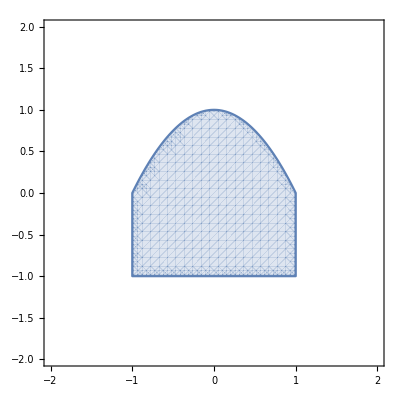

```mathematica
Clear[x,y,z];
(* surface formula (upper y-bound of volume *)
f[x_]:=-x^2+1;
(* surface *)
surface=Plot[f[x],{x,-1,1}];
(* proper volume *)
volume=RegionPlot[
y≤f[x]
&&-1≤y≤1
&&-1≤x≤1,
{x,-1.5,1.5},{y,-1.5,1.5},
PlotPoints->30,
PlotStyle->Directive[Opacity[0.2]],
PlotRange->{{-2,2},{-2,2},{-2,2}}
];
Show[volume]
```

```mathematica
Clear[x,y,z];
slices={};
For[
i=-1,i≤1,i=i+0.1,
AppendTo[slices,ParametricPlot[
{i,y},{y,-1,f[i]},
PlotStyle->Directive[Opacity[1]]]];
];
Manipulate[Show[
Append[
Table[slices[[i]],{i,1,j}]
,volume],
PlotRange->{{-2,2},{-2,2}}
],{j,1,Length[slices]}]
(*Show[volume,slices,PlotRange->All]*)
```

Part::partd: Part specification slices⟦1⟧ is longer than depth of object.

Part::partd: Part specification slices⟦2⟧ is longer than depth of object.

Part::partd: Part specification slices⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{slices⟦1⟧,slices⟦2⟧,slices⟦3⟧,slices⟦4⟧,slices⟦5⟧,slices⟦6⟧,slices⟦7⟧,slices⟦8⟧,slices⟦9⟧,slices⟦10⟧,volume},PlotRange→{{-2,2},{-2,2}}].

Part::partd: Part specification slices⟦1⟧ is longer than depth of object.

Part::partd: Part specification slices⟦2⟧ is longer than depth of object.

Part::partd: Part specification slices⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….